```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/INI/MMB paper/figures/polymer

```mathematica
kfwd=0.1
krev=0.1
volume=1000
a0=20000
```

0.1

0.1

1000

20000

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdataend1=Import["polymer_end1out.txt","CSV"];
```

```mathematica
simdataend1;
```

```mathematica
simdataend1a=Drop[simdataend1[[-1]],1]
```

{829,658,511,424,333,296,199,161,137,104,84,76,46,40,34,40,24,14,13,12,6,7,7,2,2,1,3,3,3,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}

```mathematica
simdataend2=Import["polymer_end2out.txt","CSV"];
```

```mathematica
simdataend2;
```

```mathematica
simdataend2a=Drop[simdataend2[[-1]],1]
```

{91,151,145,135,121,105,106,86,97,74,51,49,62,48,44,32,51,35,21,33,23,28,21,18,11,14,12,21,11,12,10,6,10,10,5,4,8,4,6,10,2,2,1,1,1,0,3,1,1,3,1,1,2,0,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
simdatamid=Import["polymer_midout.txt","CSV"];
```

```mathematica
simdatamida=Drop[simdatamid[[-1]],1]
```

{676,586,464,416,312,298,225,197,133,126,70,79,60,39,35,30,13,22,16,10,5,6,1,8,3,5,2,6,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

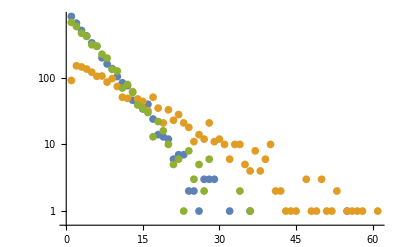

```mathematica
ListLogPlot[{simdataend1a,simdataend2a,simdatamida}]
```

```mathematica
(* Association constant *)
ka=kfwd/krev
```

1.

```mathematica
a1eq=a0*(1+2*ka*a0/volume-Sqrt[1+4*ka*a0/volume])/(2*ka^2*(a0/volume)^2)
```

800.

```mathematica
theory[n_]=a1eq*(ka*a1eq/volume)^(n-1)
```

800. 0.8^(-1+n)

```mathematica
theoryhigh[n_]=theory[n]+Sqrt[theory[n]]
```

800. 0.8^(-1+n)+28.2843 √(0.8^(-1+n))

```mathematica
theorylow[n_]=theory[n]-Sqrt[theory[n]]
```

800. 0.8^(-1+n)-28.2843 √(0.8^(-1+n))

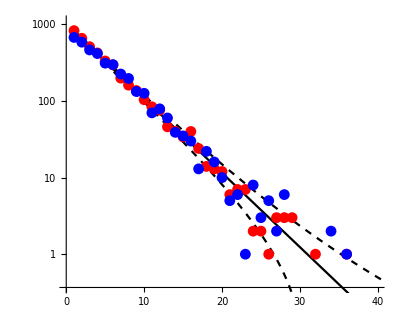

```mathematica
Show[{LogPlot[theory[n],{n,1,50},PlotStyle->Black],
LogPlot[theoryhigh[n],{n,1,50},PlotStyle->{Black,Dashed}],
LogPlot[theorylow[n],{n,1,50},PlotStyle->{Black,Dashed}],
ListLogPlot[simdataend1a,PlotStyle->Red],
ListLogPlot[simdatamida,PlotStyle->Blue]},
PlotRange->{{0,40},{-1,7}},AxesOrigin->{0,-1},AxesStyle->Bold,AspectRatio->0.8]
```

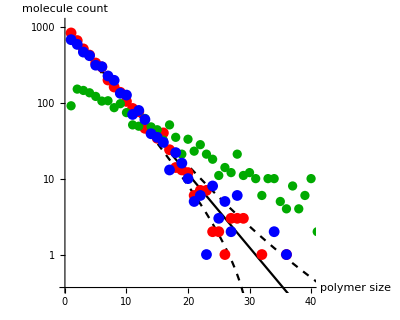

```mathematica
Show[{LogPlot[theory[n],{n,1,50},PlotStyle->Black],
LogPlot[theoryhigh[n],{n,1,50},PlotStyle->{Black,Dashed}],
LogPlot[theorylow[n],{n,1,50},PlotStyle->{Black,Dashed}],
ListLogPlot[simdataend1a,PlotStyle->Red],
ListLogPlot[simdataend2a,PlotStyle->Darker[Green]],
ListLogPlot[simdatamida,PlotStyle->Blue]},
PlotRange->{{0,40},{-1,7}},AxesOrigin->{0,-1},AxesStyle->Bold,AspectRatio->0.8,AxesLabel->{"polymer size","molecule count"}]
```